```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

## Basic Channels with Switch

Defining Pauli Matrices:

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

We have 3 Lindblad coefficients as gamma1, gamma2 and gamma3. The equations involving these coefficients have the form of Integration of  gamma1 + gamma2 and Integration of gamma2 + gamma3. Also we can choose these to be constant, independent of time. The terms we get after integration are:

```mathematica
γ1 = 1;
γ2 = 1;
ξa1= γ1*t;
ξa2=(γ1+γ2)t;
```

Depending on how terms factor out in the dynamical map, we define following:

```mathematica
Aa1=(1+Exp[-4ξa1])/2;
Aa2=(1-Exp[-4ξa1])/2;
Aa3=Exp[-2ξa2];
θ=0;
```

Now from the dynamical map, we find the following Kraus representation:

```mathematica
Kra[0]=Sqrt[Aa2]*({{0, 1}, {0, 0}})
Kra[1]=Sqrt[Aa2]*({{0, 0}, {1, 0}})
Kra[2]=Sqrt[(Aa1+Aa3)/2]*({{Exp[ⅈ*θ], 0}, {0, 1}})
Kra[3]=Sqrt[(Aa1-Aa3)/2]*({{-Exp[ⅈ*θ], 0}, {0, 1}})
```

We check if these Kraus operators satisfy the identity condition:

```mathematica
MatrixForm[Simplify[Sum[Transpose[Kra[i]].Kra[i],{i,0,3}]]];
Eigenvalues[Sum[KroneckerProduct[σ0,Kra[i]].{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}.Transpose[KroneckerProduct[σ0,Kra[i]]],{i,0,3}]];
```

Now we define a general initial density matrix and find its time evolution using the Kraus operator formulation:

```mathematica
ρ=({{ρ11, ρ12}, {ρ21, ρ22}});
ρt=Sum[Kra[i].ρ.Transpose[Kra[i]],{i,0,3}];
MatrixForm[ρt]
```

(1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ11+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ11+1/2 (1-ⅇ^(-4 t)) ρ22 | -1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ12+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ12
-1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ21+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ21 | 1/2 (1-ⅇ^(-4 t)) ρ11+1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ22+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) ρ22)

```mathematica
ρa=({{1, 0}, {0, 0}});
ρat=Sum[Kra[i].ρa.Transpose[Kra[i]],{i,0,3}];
MatrixForm[ρat]
```

(1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t)))+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))) | 0
0 | 1/2 (1-ⅇ^(-4 t)))

```mathematica
ρb=({{0, 0}, {0, 1}});
ρbt=Sum[Kra[i].ρb.Transpose[Kra[i]],{i,0,3}];
MatrixForm[ρbt]
```

(1/2 (1-ⅇ^(-4 t)) | 0
0 | 1/2 (-ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t)))+1/2 (ⅇ^(-4 t)+1/2 (1+ⅇ^(-4 t))))

```mathematica
Dist=Simplify[Tr[Sqrt[Transpose[ρat-ρbt].(ρat - ρbt)]]/2]
```

√(ⅇ^(-8 t))

Now we are going to define the basis states for the order in which channels Kraus operators could be applied, m1[0] for |0><0| and m1[1] for |1><1|

```mathematica
m1[0]={{1,0},{0,0}};
m1[1]={{0,0},{0,1}};
```

We are taking the control qubit in the |+><+| state whose matrix representation would be:

```mathematica
ω1 = {{1/2,1/2},{1/2,1/2}};
MatrixForm[ω1];
```

Now we are going to find the time evolution of the states defined above when we apply the Switch operation. First step is to find the tensor product of our system state with the control qubit.

```mathematica
ρKPω1 = KroneckerProduct[ρ, ω1];
ρaKPω1 = KroneckerProduct[ρa, ω1];
ρbKPω1 = KroneckerProduct[ρb, ω1];
```

Now we find the operators corresponding to different permutations of Kraus operators:

```mathematica
For[i=0,i<4,i++,For[j=0,j<4,j++,order[i,j,0]=KroneckerProduct[(Kra[i].Kra[j]),m1[0]]]];
For[i=0,i<4,i++,For[j=0,j<4,j++,order[i,j,1]=KroneckerProduct[(Kra[i].Kra[j]),m1[1]]]];
For[i=0,i<4,i++,For[j=0,j<4,j++,S[i,j]=order[i,j,0]+order[j,i,1]]];
STable = Table[S[i,j], {i,4},{j,4}]
```

The following expressions represent the time evolution of rho, rhoa and rhob along with the control qubit. KP stands for Kronecker Product.

```mathematica
Switch1ρKPω1=FullSimplify[Refine[Sum[S[i,j].ρKPω1.Transpose[S[i,j]],{i,0,3},{j,0,3}]]];
Switch1ρaKPω1 =FullSimplify[Refine[Sum[S[i,j].ρaKPω1.Transpose[S[i,j]],{i,0,3},{j,0,3}]]]
Switch1ρbKPω1 =FullSimplify[Refine[Sum[S[i,j].ρbKPω1.Transpose[S[i,j]],{i,0,3},{j,0,3}]]];
```

{{1/4 (1+ⅇ^(-8 t)),1/8 ⅇ^(-8 t) (1+ⅇ^(4 t))^2,0,0},{1/8 ⅇ^(-8 t) (1+ⅇ^(4 t))^2,1/4 (1+ⅇ^(-8 t)),0,0},{0,0,1/4-ⅇ^(-8 t)/4,ⅇ^(-6 t) Sinh[2 t]},{0,0,ⅇ^(-6 t) Sinh[2 t],1/4-ⅇ^(-8 t)/4}}

Now we are going to make the measurement on the control qubit. For that we define the bases in which the measurement is to be done:

```mathematica
mb1[0]={{1/(√2),1/(√2)}};
mb1[1]={{ 1/(√2),-1/(√2)}};
```

Since we are are only making measurement on the control qubit, we define the measurement operators, mo, as follows:

```mathematica
Refine[For[i=0,i<2,i++,mo1[i]=KroneckerProduct[({{1, 0}, {0, 1}}),mb1[i]]]];
Refine[For[i=0,i<2,i++,sysρ1[i]=mo1[i].Switch1ρKPω1.Transpose[mo1[i]]]];
Refine[For[i=0,i<2,i++,sysρa1[i]=mo1[i].Switch1ρaKPω1.Transpose[mo1[i]]]];
Refine[For[i=0,i<2,i++,sysρb1[i]=mo1[i].Switch1ρbKPω1.Transpose[mo1[i]]]];
```

Now we find the expressions for system density operator by making the measurement in the |+><+| basis:

```mathematica
ρf1[0]=Simplify[sysρ1[0]/Tr[sysρ1[0]]];
MatrixForm[ρf1[0]]
```

(((3+2 ⅇ^(4 t)+3 ⅇ^(8 t)) ρ11+2 (-3+2 ⅇ^(4 t)+ⅇ^(8 t)) ρ22)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)) (ρ11+ρ22)) | ((9-2 ⅇ^(4 t)+ⅇ^(8 t)) ρ12)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)) (ρ11+ρ22))
((9-2 ⅇ^(4 t)+ⅇ^(8 t)) ρ21)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)) (ρ11+ρ22)) | (2 (-3+2 ⅇ^(4 t)+ⅇ^(8 t)) ρ11+(3+2 ⅇ^(4 t)+3 ⅇ^(8 t)) ρ22)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)) (ρ11+ρ22)))

When measured in the |-><-|, we get:

```mathematica
ρf1[1]=Simplify[sysρ1[1]/Tr[sysρ1[1]]];
MatrixForm[ρf1[1]]
```

((ρ11+2 ρ22)/(3 (ρ11+ρ22)) | -ρ12/(3 (ρ11+ρ22))
-ρ21/(3 (ρ11+ρ22)) | (2 ρ11+ρ22)/(3 (ρ11+ρ22)))

```mathematica
ρaf1[0]=Simplify[sysρa1[0]/Tr[sysρa1[0]]];
ρaf1[1]=Simplify[sysρa1[1]/Tr[sysρa1[1]]];
ρbf1[0]=Simplify[sysρb1[0]/Tr[sysρb1[0]]];
ρbf1[1]=Simplify[sysρb1[1]/Tr[sysρb1[1]]];
X1=Tr[Sqrt[Transpose[((ρaf1[0]+ρaf1[1])-(ρbf1[0]+ρbf1[1]))].((ρaf1[0]+ρaf1[1])-(ρbf1[0]+ρbf1[1]))]]/2
```

1/2 (√((1/3+(2 (-3+2 ⅇ^(4 t)+ⅇ^(8 t)))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t))-(3+2 ⅇ^(4 t)+3 ⅇ^(8 t))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)))^2)+√((-1/3-(2 (-3+2 ⅇ^(4 t)+ⅇ^(8 t)))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t))+(3+2 ⅇ^(4 t)+3 ⅇ^(8 t))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)))^2))

```mathematica
For[i=0,i<2,i++, DistSwitch1[i]=Simplify[Tr[Sqrt[Transpose[(ρaf1[i]-ρbf1[i])].(ρaf1[i]-ρbf1[i])]]/2]];
```

```mathematica
Clear[t];
ρbf1[1]
```

{{2/3,0},{0,1/3}}

```mathematica
Somematrix[t_] = {{(3+2 ⅇ^(4 t)+3 ⅇ^(8 t))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t)),0},{0,(2 (-3+2 ⅇ^(4 t)+ⅇ^(8 t)))/(-3+6 ⅇ^(4 t)+5 ⅇ^(8 t))}};
Somematrix[0]
```

{{1,0},{0,0}}

```mathematica
DistSwitch1[0]
```

√(((9-2 ⅇ^(4 t)+ⅇ^(8 t))^2)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t))^2))

```mathematica
DistSwitch1[1]
```

1/3

```mathematica
√(((-4 ⅇ^(2 t γ1)+3 ⅇ^(2 t γ2)+ⅇ^(2 t (2 γ1+γ2)))^2)/((-4 ⅇ^(2 t γ1)+ⅇ^(2 t γ2)+3 ⅇ^(2 t (2 γ1+γ2)))^2))
```

√(((-ⅇ^(2 t)+ⅇ^(6 t))^2)/((-3 ⅇ^(2 t)+3 ⅇ^(6 t))^2))

## Let’s Define a 2nd order Switch

Let’s do it first in 2 basis where we will consider only one of the orders available to the 2nd order switch, so that we need only 2 states for the order in which the Kraus operators for 2nd order switch can be defined: So let’s choose m2[0] for |0><0| and m2[1] for |1><1|. These basis did not have to be same as the one defined for 1st order switch.

```mathematica
m2[0]={{1,0},{0,0}};
m2[1]={{0,0},{0,1}};
```

Now we need to define the state of the control qubit for this superposition, which can in principle be different from the previous one. But for simplicity, let’s take the control qubit in the |+><+| state whose matrix representation would be:

```mathematica
ω2 = {{1/2,1/2},{1/2,1/2}};
MatrixForm[ω2];
```

Now we are going to define the Switch operator corresponding to 2nd order Switch:

```mathematica
order0[i_,j_,k_,l_]=KroneckerProduct[(S[i, j].S[k,l]),m2[0]];
order1[i_,j_,k_,l_]=KroneckerProduct[(S[k, l].S[i,j]),m2[1]];
S2[i_,j_,k_,l_]=order0[i,j,k,l]+order1[i,j,k,l];
```

```mathematica
S2Table = Table[S2[i,j,k,l],{i,0,3},{j,0,3},{k,0,3},{l,0,3}];
TS2Table = Table[Transpose[S2[i,j,k,l]],{i,0,3},{j,0,3},{k,0,3},{l,0,3}];
S2Table
Dimensions[TS2Table]
```

{{{1},{{1},{1},{1},{1}},{{1},{1},{1+1,3},{1}},{1}},{1},1,{1}}
 |  |  |  |

{4,4,4,4}

The following expressions represent the time evolution of rho, rhoa and rhob along with the control qubits, omega1 and omega2. KP stands for Kronecker Product.

```mathematica
Switch2ρKPω1KPω2=FullSimplify[Refine[Sum[Part[S2Table,i,j,k,l].KroneckerProduct[ρ, ω1, ω2].Part[TS2Table,i,j,k,l],{i,4},{j,4},{k,4},{l,4}]]];
FullSimplify[MatrixForm[Switch2ρKPω1KPω2]]
```

```mathematica
Switch2ρaKPω1KPω2 =FullSimplify[Refine[Sum[Part[S2Table,i,j,k,l].KroneckerProduct[ρa, ω1, ω2].Part[TS2Table,i,j,k,l],{i,4},{j,4},{k,4},{l,4}]]];
FullSimplify[MatrixForm[Switch2ρaKPω1KPω2]]
```

```mathematica
Switch2ρbKPω1KPω2 =FullSimplify[Refine[Sum[Part[S2Table,i,j,k,l].KroneckerProduct[ρb, ω1, ω2].Part[TS2Table,i,j,k,l],{i,4},{j,4},{k,4},{l,4}]]];
FullSimplify[MatrixForm[Switch2ρbKPω1KPω2]]
```

Now we are going to make the measurement on control qubits. Since there are two of them, so in principle we could define two distinct measurement basis. But again for simplicity we are taking them to be same.

```mathematica
mb2[0]={{1/(√2),1/(√2)}};
mb2[1]={{ 1/(√2),-1/(√2)}};
```

Now we have four different possibilities, corresponding to basis on which we make measurement on the control qubit. We define the measurement operators, mo, as follows:

```mathematica
Refine[For[i=0,i<2,i++, For[j = 0, j < 2, j++, mo2[i,j]=KroneckerProduct[({{1, 0}, {0, 1}}),mb1[i], mb2[j]]]]];
Refine[For[i=0,i<2,i++,For[j = 0, j < 2, j++,sysρ2[i, j]=mo2[i, j].Switch2ρKPω1KPω2.Transpose[mo2[i, j]]]]];
Refine[For[i=0,i<2,i++,For[j = 0, j < 2, j++,sysρa2[i, j]=mo2[i, j].Switch2ρaKPω1KPω2.Transpose[mo2[i, j]]]]];
Refine[For[i=0,i<2,i++,For[j = 0, j < 2, j++,sysρb2[i, j]=mo2[i, j].Switch2ρbKPω1KPω2.Transpose[mo2[i, j]]]]];
MatrixForm[Simplify[sysρ2[0,0]]]
MatrixForm[Simplify[sysρ2[0,1]]](* The measured unnormalised ρ^SWITCH for +- is Subscript[0, 2*2]! Is it possible? What are the consequences?*)
MatrixForm[Simplify[sysρ2[1,0]]](* The measured unnormalised ρ^SWITCH for -+ is Subscript[0, 2*2]! Is it possible? What are the consequences?*)
MatrixForm[Simplify[sysρ2[1,1]]](* The measured unnormalised ρ^SWITCH for -- is Subscript[0, 2*2]! Is it possible? What are the consequences?*)
```

Let us see the expression for the final state of the general state when we make the measurement in |+><+| basis on both the control qubits:

```mathematica
ρf2[0,0]=Simplify[sysρ2[0,0]/Tr[sysρ2[0,0]]];
MatrixForm[ρf2[0,0]]
```

({{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,1/2,1/2}}.(16 (1)).{{1/2,0},6,{0,1/2}})/Tr[{{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,1/2,1/2}}.(16 1).{{1/2,0},6,{0,1/2}}]
 |  |  |  |

When measured in the |-><-| basis for both the qubits, we get

```mathematica
ρf2[1,1]=sysρ2[1,1]/Tr[sysρ2[1,1]];
MatrixForm[ρf2[1,1]](*The matrix is Subscript[0, 2*2] but since it was tried to be normalised by Trace=0, it becomes indeterminate*)
```

({{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,0,0,0,1/2,-1/2,-1/2,1/2}}.(16 1).{{1/2,0},6,{0,1/2}})/Tr[{{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,0,0,0,1/2,-1/2,-1/2,1/2}}.1.{{1/2,0},6,{0,1}}]
 |  |  |  |

```mathematica
ρaf2[i_,j_]=Simplify[sysρa2[i,j]/Tr[sysρa2[i,j]]];
ρaf2[0, 1]=Simplify[sysρa2[0,1]/Tr[sysρa2[0,1]]];
ρaf2[1, 0]=Simplify[sysρa2[1,0]/Tr[sysρa2[1,0]]];
ρaf2[1, 1]=Simplify[sysρa2[1,1]/Tr[sysρa2[1,1]]];
ρbf2[0,0]=Simplify[sysρb2[0,0]/Tr[sysρb2[0,0]]];
ρbf2[0,1]=Simplify[sysρb2[0,1]/Tr[sysρb2[0,1]]];
ρbf2[1,0]=Simplify[sysρb2[1,0]/Tr[sysρb2[1,0]]];
ρbf2[1,1]=Simplify[sysρb2[1,1]/Tr[sysρb2[1,1]]];
```

Now there will be 4 distance functions:

```mathematica
For[i=0,i<2,i++, For[j = 0, j < 2, j++, DistSwitch2[i,j]=Simplify[Tr[Sqrt[Transpose[(ρaf2[i,j]-ρbf2[i,j])].(ρaf2[i,j]-ρbf2[i,j])]]/2]]];
```

Earlier when we calculated trace distance b/w the states, we measurement was done in |+><+| basis, let’s see the behavior of trace distance when measurement is done in |-><-| basis as well:

```mathematica
DistSwitch2[0,0]
```

1/2 Tr[√(Transpose[-1/Tr[{{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,4,1/2,1/2}}.1.{1}]+sysρa2[2,2]/Tr[sysρa2[2,2]]].(-1/Tr[1]+1))]
 |  |  |  |

Let’s make the following substitutions:

```mathematica
ρ22 = 1 - ρ11;
ρ12 = ρ21;
γ1 = γ2 = 1;
```

After having these values, let’s see the expressions for Distance b/w these states in 1st and 2nd order:

```mathematica
DistSwitch1[0]
```

√(((9-2 ⅇ^(4 t)+ⅇ^(8 t))^2)/((-3+6 ⅇ^(4 t)+5 ⅇ^(8 t))^2))

```mathematica
DistSwitch1[1]
```

1/3

```mathematica
DistSwitch2[0,0]
```

1/2 Tr[√(Transpose[-1/Tr[{{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,4,1/2,1/2}}.1.{1}]+sysρa2[2,2]/Tr[sysρa2[2,2]]].(-1/Tr[1]+1))]
 |  |  |  |

```mathematica
DistSwitch2[0,1]
```

1/2 Tr[√(Transpose[-({{1/2,-1/2,1/2,-1/2,0,0,0,0},{0,0,4,1/2,-1/2}}.(1).{1})/Tr[1]+1/Tr[1]].(-1/Tr[1]+1))]
 |  |  |  |

```mathematica
DistSwitch2[1,0]
```

1/2 Tr[√(Transpose[-({{1/2,1/2,-1/2,-1/2,0,0,0,0},{0,6,-1/2}}.(16 1).{1})/Tr[{{1/2,1/2,-1/2,-1/2,0,0,0,0},{0,6,-1/2}}.(1).{1}]+1].1)]
 |  |  |  |

```mathematica
DistSwitch2[1,1]
```

1/2 Tr[√(Transpose[-({{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,6,1/2}}.(16 1).{1})/Tr[{{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,6,1/2}}.(1).{1}]+1].1)]
 |  |  |  |

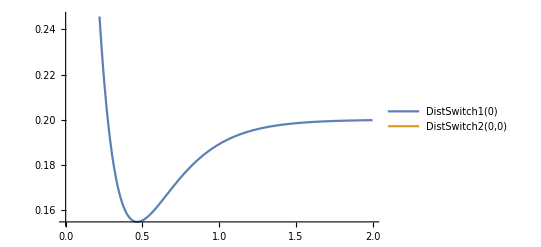

```mathematica
Plot[{DistSwitch1[0],DistSwitch2[0,0]},{t,0,2},PlotLegends->"Expressions"]
```

```mathematica
Simplify[DistSwitch1[1]]
```

1/3

## Let’s Define a 3rd order Switch

Let’s do it first in 2 basis where we will consider only one of the orders available to the 3rd order switch, so that we need only 2 states for the order in which the Kraus operators for 3rd order switch can be defined: So let’s choose m3[0] for |0><0| and m3[1] for |1><1|. These basis did not have to be same as the one defined for 1st and 2nd order switch.

```mathematica
Clear[i];
Clear[j];
Clear[k];
Clear[l];
m3[0]={{1,0},{0,0}};
m3[1]={{0,0},{0,1}};
```

Now we need to define the state of the control qubit for this superposition, which can in principle be different from the previous one. But for simplicity, let’s take the control qubit in the |+><+| state whose matrix representation would be:

```mathematica
ω3 = {{1/2,1/2},{1/2,1/2}};
MatrixForm[ω3];
```

Now we are going to define the Switch operator corresponding to 3rd order Switch:

```mathematica
S3order1[i_,j_,k_,l_,m_,n_,o_,p_] = KroneckerProduct[(S2[i,j,k,l].S2[m,n,o,p]),m3[0]];
S3order2[i_,j_,k_,l_,m_,n_,o_,p_] = KroneckerProduct[(S2[m,n,o,p].S2[i,j,k,l]),m3[1]];
S3[i_,j_,k_,l_,m_,n_,o_,p_]=Simplify[S3order1[i,j,k,l,m,n,o,p]+S3order2[i,j,k,l,m,n,o,p]];
S3Table = Table[S3[i,j,k,l,m,n,o,p],{i, 0,3}, {j, 0,3}, {k, 0,3}, {l, 0,3},{m,0,3},{n,0,3},{o,0,3},{p,0,3}];
TS3[i_,j_,k_,l_,m_,n_,o_,p_] = Transpose[S3[i,j,k,l,m,n,o,p]];
TS3Table = Table[TS3[i,j,k,l,m,n,o,p],{i, 0,3}, {j, 0,3}, {k, 0,3}, {l, 0,3},{m,0,3},{n,0,3},{o,0,3},{p,0,3}];
(*Refine[FullSimplify[S3[0,1,0,1,0,1,0,1]]]
TS3[0,1,0,1,0,1,0,1]
Dimensions[S3Table]
Dimensions[TS3Table]*)
```

The following expression represents the time evolution of ρ, ρa and ρb along with the control qubits, ω1 and ω2. KP stands for Kronecker Product.

```mathematica
Switch3ρKPω1KPω2KPω3=FullSimplify[Refine[Sum[Part[S3Table,1,i,j,k,l,m,n,o,p].KroneckerProduct[ρ,ω1,ω2,ω3].Part[TS3Table,1,i,j,k,l,m,n,o,p],{i,4},{j,4},{k,4},{l,4},{m,4},{n,4},{o,4},{p,4}]]];
```

Part::partw: Part 2 of Transpose[KroneckerProduct[(KroneckerProduct[{«4»}.S[«2»],{{«2»},{«2»}}]+KroneckerProduct[S[«2»].{«4»},{{«2»},{«2»}}]).(KroneckerProduct[{«4»}.S[«2»],{{«2»},{«2»}}]+KroneckerProduct[S[«2»].{«1»},«1»]),{«1»}]+«1»] does not exist.

Part::partw: Part 3 of KroneckerProduct[(KroneckerProduct[{{«4»},{«4»},{«4»},{«4»}}.S[2,4],{{0,0},{0,1}}]+KroneckerProduct[S[2,4].{{«4»},{«4»},{«4»},{«4»}},{{1,0},{0,0}}]).(KroneckerProduct[«1».S[2,4],{{0,0},{0,1}}]+«1»),{«1»,«1»}]+«1» does not exist.

Part::partw: Part 3 of Transpose[KroneckerProduct[(KroneckerProduct[{«4»}.S[«2»],{{«2»},{«2»}}]+KroneckerProduct[S[«2»].{«4»},{{«2»},{«2»}}]).(KroneckerProduct[{«4»}.S[«2»],{{«2»},{«2»}}]+KroneckerProduct[S[«2»].{«1»},«1»]),{«1»}]+«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Switch3ρaKPω1KPω2KPω3=FullSimplify[Refine[Sum[Part[S3Table,1,i,j,k,l,m,n,o,p].KroneckerProduct[ρa,ω1,ω2,ω3].Part[TS3Table,1,i,j,k,l,m,n,o,p],{i,4},{j,4},{k,4},{l,4},{m,4},{n,4},{o,4},{p,4}]]];
```

```mathematica
Switch3ρbKPω1KPω2KPω3=FullSimplify[Refine[Sum[Part[S3Table,1,i,j,k,l,m,n,o,p].KroneckerProduct[ρb,ω1,ω2,ω3].Part[TS3Table,1,i,j,k,l,m,n,o,p],{i,4},{j,4},{k,4},{l,4},{m,4},{n,4},{o,4},{p,4}]]];
```

Now we are going to make the measurement on control qubits. Since there are two of them, so in principle we could define two distinct measurement basis. But again for simplicity we are taking them to be same.

```mathematica
mb3[0]={{1/(√2),1/(√2)}};
mb3[1]={{ 1/(√2),-1/(√2)}};
```

Now we have eight different possibilities, corresponding to basis on which we make measurement on the control qubit. We define the measurement operators, m_o, as follows:

```mathematica
mo3[x_,y_,z_]=KroneckerProduct[({{1, 0}, {0, 1}}),mb1[x], mb2[y],mb3[z]];Refine[sysρ3[x_,y_,z_]=mo3[x,y,z].Switch3ρKPω1KPω2KPω3.Transpose[mo3[x,y,z]]];
Refine[sysρa3[x_,y_,z_]=mo3[x,y,z].Switch3ρaKPω1KPω2KPω3.Transpose[mo3[x,y,z]]];
Refine[sysρb3[x_,y_,z_]=mo3[x,y,z].Switch3ρbKPω1KPω2KPω3.Transpose[mo3[x,y,z]]];
(*MatrixForm[Simplify[sysρ3[0,0,0]]]*)
(*MatrixForm[Simplify[sysρ2[0,1]]](* The measured unnormalised ρ^SWITCH for +- is Subscript[0, 2*2]! Is it possible? What are the consequences?*)
MatrixForm[Simplify[sysρ2[1,0]]](* The measured unnormalised ρ^SWITCH for -+ is Subscript[0, 2*2]! Is it possible? What are the consequences?*)
MatrixForm[Simplify[sysρ2[1,1]]](* The measured unnormalised ρ^SWITCH for -- is Subscript[0, 2*2]! Is it possible? What are the consequences?*)*)
```

Let us see the expression for the final state of the general state when we make the measurement in |+><+| basis on both the control qubits:

```mathematica
ρf3[x_,y_,z_]=Simplify[sysρ3[x,y,z]/Tr[sysρ3[x,y,z]]];
ρfa3[x_,y_,z_]=Simplify[sysρa3[x,y,z]/Tr[sysρa3[x,y,z]]];
ρfb3[x_,y_,z_]=Simplify[sysρb3[x,y,z]/Tr[sysρb3[x,y,z]]];
MatrixForm[ρf3[0,0,0]]
MatrixForm[ρfa3[0,0,0]]
MatrixForm[ρfb3[0,0,0]]
```

{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}}.(1/8 ⅇ^(-16 t) ρ11 (2+5 Cosh[4 t]+4 Cosh[8 t]+5 Cosh[12 t]) Sinh[2 t]^2).{{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}}/Tr[{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}}.(1/8 ⅇ^(-16 t) ρ11 (2+5 Cosh[4 t]+4 Cosh[8 t]+5 Cosh[12 t]) Sinh[2 t]^2).{{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}}]

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

Dot::dotsh: Tensors {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} and {{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}} have incompatible shapes.

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

1
 |  |  |  |

{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}}.0.{{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}}/Tr[{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}}.0.{{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}}]

Now there will be 8 distance functions:

```mathematica
DistSwitch3[x_,y_,z_]=Simplify[Tr[Sqrt[Transpose[(ρfa3[x,y,z]-ρfb3[x,y,z])].(ρfa3[x,y,z]-ρfb3[x,y,z])]]/2];
```

Earlier when we calculated trace distance b/w the states, we measurement was done in |+><+| basis, let’s see the behavior of trace distance when measurement is done in |-><-| basis as well:

```mathematica
DistSwitch3[0,0,0]
```

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

Dot::dotsh: Tensors {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} and {{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}} have incompatible shapes.

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

1/2 Tr[√(Transpose[-({{1/(2 √2),14,0},{0,14,1/1}}.11{1})/Tr[1]+1/Tr[1]].(-1/1+1))]
 |  |  |  |

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

Dot::dotsh: Tensors {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} and {{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{1/(2 √2),0},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)},{0,1/(2 √2)}} have incompatible shapes.

Dot::dotsh: Tensors {{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}} and {{{{«1»},{«1»},{«1»},{«1»}},{«1»},{«1»},«1»},{{«1»},{{«1»},{«1»},{«1»},{«1»}},{{«1»},{«1»},{{«1»},«2»,{{{{«4»},{«4»},{«4»},{«4»}},«1»,{{«4»},«2»,{«4»}},{{«4»},{«4»},{«4»},{«4»}}},«3»}},{«1»}},{«1»}},{«1»},{«1»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

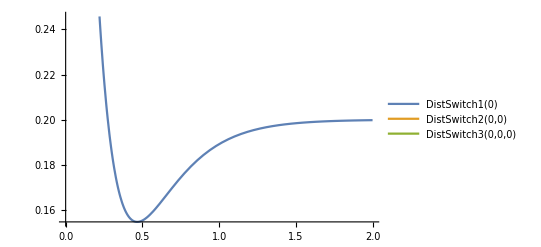

```mathematica
Plot[{DistSwitch1[0],DistSwitch2[0,0], DistSwitch3[0,0,0]},{t,0,2},PlotLegends->"Expressions"]
```